Ultra-intense laser pulse characterization using ponderomotive electron scattering

Felix Mackenroth, Amol R Holkundkar and Hans-Peter Schlenvoigt, New J. Phys. 21 (2019) 123028
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper. 

Focus dominated ponderomotive scattering: W0/zR=λ/(π W0) > √2 a0/ <γ> , “low laser power” -> harmonic oscillator

Amplitude dominated ponderomotive scattering: W0/zR=λ/(π W0) < √2 a0/ <γ> -> exponentially accelerated 2nd order ODE

Frequency parameter Ω is defined in equation 15

## Equation14: harmonic oscillator or exponential acceleration

```mathematica
(* this would be the 1st derivative in xprp *)
Clear[ξprp,τ,c,t,lR,t,xprp,eq]
ξprp[t_]:=xprp[t]/Sqrt[1+(c t/lR)^2];
τ=lR (ArcTan[c t/lR]+π/2);

(* equation 13 *)
(*D[ξprp,τ]=D[ξprp,t] D[t,τ]*)
D[ξprp[t],t]/D[τ,t]-((Sqrt[1+(c t/lR)^2]-c t ξprp[t]/lR^2))//FullSimplify
```

(√(1+(c^2 t^2)/lR^2) (-c+xprp'[t]))/c

```mathematica
(* get 2nd term of LHS of eq 14 *)
Clear[ξprp,τ,c,t,lR,t,xprp,eq,d2ξd2τ]
t=lR/c Tan[τ/lR-π/2];
(* differentiate equation 13 *)
d2ξd2τ=D[Sqrt[1+(c t/lR)^2]-c t ξprp[τ]/lR^2,τ];
(* replace again with eq 13 *)
d2ξd2τ/.{ξprp'[τ]->(Sqrt[1+(c t/lR)^2]- c t ξprp/lR^2),ξprp[τ]->ξprp}//FullSimplify
```

-ξprp/lR^2

## Transverse profile

1/2 √π Erf[1]

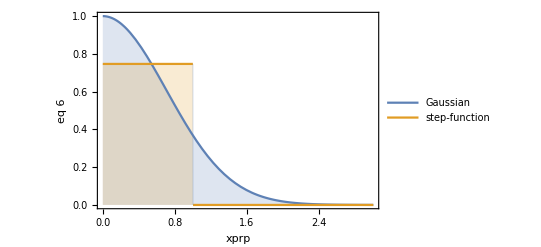

```mathematica
Clear[xprp,W]
(* equation 6 *)
1/W Integrate[Exp[-(xprp/W)^2],{xprp,0,W}]

W=1;
Plot[{Exp[-(xprp/W)^2],Sqrt[π/4]Erf[1]HeavisideTheta[W-xprp]},{xprp,0,3W},Frame->True,FrameLabel->{"xprp","eq 6"},PlotLegends->{"Gaussian","step-function"},Filling->Bottom]
```

## Equation 23

```mathematica
Clear[ν]
FindRoot[{Tan[ν]-ν/(1-ν^2)==0},{ν,2.5}]
Plot[Tan[ν]-ν/(1-ν^2),{ν,0,3}];
```

{ν→2.74371}

## Figure 2

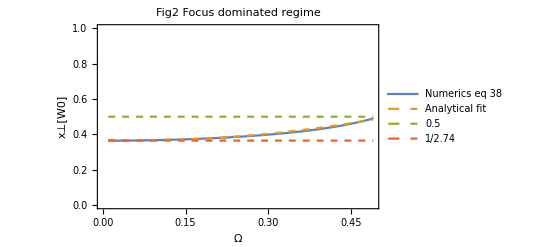

```mathematica
Clear[xW0,Ω,nu]
(*
(*start root find at nu=2 which is the first root*)
Ω=0.45;
Plot[Tan[ArcSin[Ω nu]/Ω]-(nu Sqrt[1-(Ω nu)^2])/(1-nu^2),{nu,0,10}]
*)

(* equation 38 *)
getnu[Ω_]:=1/FindRoot[Tan[ArcSin[Ω nu]/Ω]-(nu Sqrt[1-(Ω nu)^2])/(1-nu^2),{nu,2}][[1,2]]
Plot[{getnu[Ω],0.37-8 10^-2 Ω +0.64 Ω^2,0.5,1/2.74},{Ω,0.01,0.49},PlotRange->{0,1},PlotStyle->{Default,Dashed,Dashed,Dashed},Frame->True,FrameLabel->{"Ω","x⊥[W0]"},PlotLegends->{"Numerics eq 38","Analytical fit","0.5","1/2.74"},PlotLabel->"Fig2 Focus dominated regime"]
```

## Figure 3

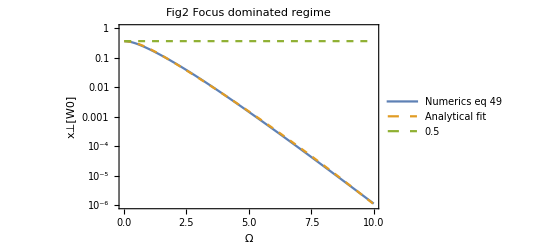

```mathematica
Clear[xW0,Ω,nu,getnu]
(*
(*start root search at analytical fit *)
Ω=5;
Plot[Tan[ArcSinh[Ω nu]/Ω]-(nu Sqrt[1+(Ω nu)^2])/(1-nu^2),{nu,0.9/(1/2.74 1/Cosh[3.8 10^-2+1.12Ω+2.2 10^-2 Ω^2]),1000}]
*)
(* in eq 49 the minus sign in nominator RHS should be + and not - *)
getnu[Ω_]:=1/FindRoot[Tan[ArcSinh[Ω nu]/Ω]-(nu Sqrt[1+(Ω nu)^2])/(1-nu^2),{nu,0.9/(1/2.74(1/Cosh[3.8 10^-2+1.12Ω+2.2 10^-2 Ω^2]))}][[1,2]]
LogPlot[{getnu[Ω],1/2.74 1/Cosh[3.8 10^-2+1.12Ω+2.2 10^-2 Ω^2],1/2.74},{Ω,0.01,9.99},PlotRange->{10^-6,10^0},PlotStyle->{Default,Dashed,Dashed,Dashed},Frame->True,FrameLabel->{"Ω","x⊥[W0]"},PlotLegends->{"Numerics eq 49","Analytical fit","0.5","1/2.74"},PlotLabel->"Fig2 Focus dominated regime"]
```

## Figure 4

from focus 4(a) to detector 4(b)

```mathematica
Clear[x,θtmax,d]
θtmax=4.4 10^-2;(* [], as it appears in the text *)
d=0.2;(*[m] detector is 20 cm from laser focus *)
x=d Tan[θtmax](* transverse distance at the detector ~ 22mm *)
```

0.00880568

Plot

```mathematica
Clear[a0,ϵi,W0,λ,lR]
a0=10;(*[]*)
ϵi=200m;(*[?]*)
W0=2.5;(*[μm]*)
λ=0.8;(*[μm]*)
lR=π W0^2/λ;
(*ArcTan[W0/lR]*)
xprp0=10W0;
```

0.101509

## Equation 47...

```mathematica
Clear[W0,Ω,xprp0,eq47,tmax,lR,gtil,tmax,θtmax,diff,λ,a0,γ0,γavg]
λ=0.8;
lR=π W0^2/λ;
γavg=Sqrt[1+a0^2+γ0^2]//N;
(* equation 15 *)
Ω=Sqrt[Abs[1-2((a0 lR)/(γavg W0))^2]];
(* equation 47 *)
tmax=lR Tan[ArcSinh[(W0 Ω)/xprp0]/Ω-π/2];
(* in-line expression *)
θtmax=(tmax W0/lR +Sqrt[xprp0^2+(W0 Ω)^2])/Sqrt[lR^2+tmax^2];

(* defined after equation 47 *)
gtil[xprp_]:=ArcSinh[W0 Ω/xprp0]/Ω
(* equation 47 *)
eq47=ArcTan[W0/lR(Sqrt[(xprp0/W0)^2+Ω^2] Sin[gtil[xprp0]]- Cos[gtil[xprp0]])];

(* assign random values *)
W0=RandomReal[{0,10}];
a0=RandomReal[{0,15}];
xprp0=W0 RandomReal[{0,3}];
γ0=RandomReal[{10^3,10^4}];

(* difference *)
diff=θtmax-eq47//N
```

1.0458×10^-7

Equation 41 -> 42

```mathematica
Clear[xprp,vprp,t,Ω,lR,c,xprp0]
(* eq 41 *)
xprp=xprp0/Ω Sqrt[1+(t/lR)^2]Sinh[Ω(ArcTan[t/lR]+π/2)];
(* eq 42 *)
vprp=D[xprp,t]//Simplify

Limit[(xprp0 (lR Ω Cosh[Ω (π/2+ArcTan[t/lR])]+t Sinh[Ω (π/2+ArcTan[t/lR])]))/(lR^2 √(1+t^2/lR^2) Ω),t->∞]
```

(xprp0 (lR Ω Cosh[Ω (π/2+ArcTan[t/lR])]+t Sinh[Ω (π/2+ArcTan[t/lR])]))/(lR^2 √(1+t^2/lR^2) Ω)

(√(1/lR^2) xprp0 Sinh[1/2 (π+√(1/lR^2) lR π) Ω])/Ω

## Figure 5

√2 a0 lR/W0 <γ> ~2.08 ~2.1 , assuming <γ> ~γ0

```mathematica
Clear[lR,a0,W0,λ,lR,γ0]
a0=15;(*[]*)
γ0=200;(*[]*)
W0=5;(*[μm]*)
λ=0.8;(*[μm]*)
lR=π W0^2/λ;
√2 a0 lR /(W0 γ0)
```

2.0826

Plot...

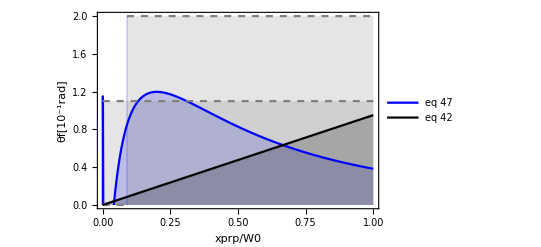

```mathematica
Clear[γavg,a0,γ0,lR,ξ,gtil,Ω,xprp,xprp0,C14,c,x0,θtmax]
lR=π W0^2/λ;
a0=10 ;(*√2*)
λ=0.8;
W0=3;
γ0=1000;
γavg=Sqrt[1+a0^2+γ0^2]//N;
C14=((2a0^2)/(γavg^2 W0^2)-1/lR^2);

(* equation 15 *)
Ω=Sqrt[Abs[1-2((a0 lR)/(γavg W0))^2]];

(* defined after equation 47 *)
gtil[xprp_]:=ArcSinh[W0 Ω/xprp0]/Ω

(* equation 47 *)
θtmax=ArcTan[W0/lR(Sqrt[(xprp0/W0)^2+Ω^2] Sin[gtil[xprp0]]- Cos[gtil[xprp0]])];

Plot[{10θtmax/.{xprp0->xprp0W0 W0},1.1,2HeavisideTheta[xprp0W0-Ω/Sinh[π Ω]],(√(1/lR^2) xprp0 Sinh[1/2 (π+√(1/lR^2) lR π) Ω])/Ω/.{xprp0->xprp0W0 W0}},{xprp0W0,0,1},PlotRange->{0,2},Filling->Bottom,PlotStyle->{Blue,Directive[Gray,Dashed],Directive[Gray,Dashed],Black},Frame->True,FrameLabel->{"xprp/W0","θf[10^-1rad]"},PlotLegends->{"eq 47","","","eq 42"}]
```

## Figure 6

```mathematica
Clear[γavg,a0,γ0,lR,ξ,gtil,Ω,xprp,xprp0]
lR=π W0^2/λ;
γavg=Sqrt[1+a0^2+γ0^2];
C14=((2a0^2)/(γavg^2 W0^2)-1/lR^2);

a0=10;
c=1;
λ=0.8;
W0=3;
γ0=1000;
x0=1;
gtil[xprp_]:=ArcSinh[W0 Ω/xprp0]

(* equation 47 *)
θtmax=ArcTan[W0/lR(Sqrt[(xprp0/W0)^2+Ω^2] Sin[gtil[xprp0]]- Cos[gtil[xprp0]])]
```

from focus 6(a) to detector 6(b)

```mathematica
Clear[x,θtmax,d]
θtmax=ArcTan[0.11];(* [], as it appears in the text *)
d=0.2;(*[m] detector is 20 cm from laser focus *)
x=d Tan[θtmax](* transverse distance at the detector ~ 22mm *)
```

0.022

## Figure 7

0.23(a0/γ)^2 instead of 0.33(a0/γ)^2 ?

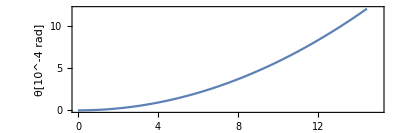

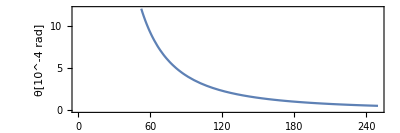

```mathematica
Clear[a0,m,γ]
γ=200 ;
Plot[{0.23 10^4 (a0/γ)^2},{a0,0,15},PlotRange->{0,12},AspectRatio->1/3,Frame->True,FrameLabel->{"a0","θ[10^-4 rad]"}]
Clear[a0,m,γ]
a0=10;
Plot[{10^3/3(a0/γ)^2},{γ,0,250},PlotRange->{0,12},AspectRatio->1/3,Frame->True,FrameLabel->{"a0","θ[10^-4 rad]"}]
```